```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
```

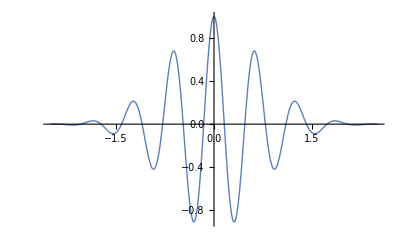

Block::lvset: Local variable specification {t = 1, ω_0 = 7} contains ω_0 = 7, which is an assignment to ω_0; only assignments to symbols are allowed.

```mathematica
Clear[e, tT, t, omega]

e[t_] := E^(-t^2/tT^2) Cos[ omega t ]

qmTwoL21Fig4 = Plot[ Block[{tT=1,omega=10},e[t]],{t,-2.5,2.5}, PlotStyle->Thick]
```

```mathematica
ft[ω_] = Distribute[FullSimplify[FourierTransform[ e[t], t, ω]]]
```

(ⅇ^(-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))+(ⅇ^(omega tT^2 ω-1/4 tT^2 (omega+ω)^2))/(2 √2 √(1/tT^2))

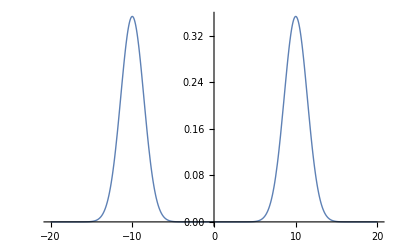

```mathematica
FTgaussianWavePacket = Plot[ Block[{tT=1,omega=10},ft[ω]],{ω,-20,20}, PlotStyle->Thick]
```

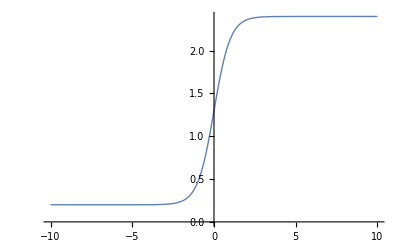

```mathematica
Plot[1.1Tanh[x] + 1.3, {x, -10, 10}, PlotStyle->Thick]
```

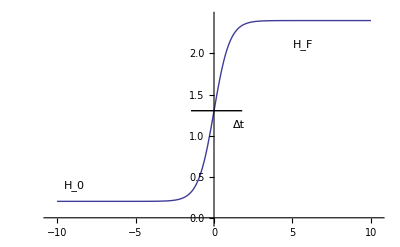

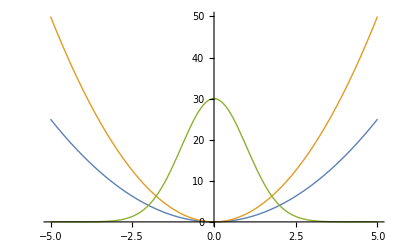

```mathematica
Plot[{ x^2, 2 x^2, 30 E^{-x^2/2}}, {x, -5, 5}, PlotStyle->Thick]
```

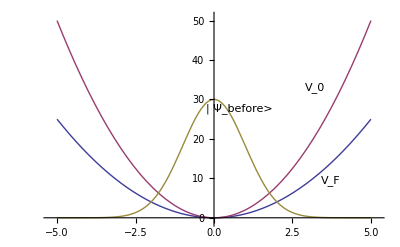

```mathematica
peeters`exportForLatex["qmTwoL21Fig4",qmTwoL21Fig4]
peeters`exportForLatex["FTgaussianWavePacket",FTgaussianWavePacket]
```

{qmTwoL21Fig4.eps,qmTwoL21Fig4pn.png}

{FTgaussianWavePacket.eps,FTgaussianWavePacketpn.png}